```mathematica
<<KerrGeodesics`
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
dtdλ[M_,a_,r_,ℰ_,ℒ_,θ_] := ℰ(((r^2+a^2)^2)/(r^2-2 M r+a^2)-a^2 Sin[θ]^2)+a ℒ(1-(r^2+a^2)/(r^2-2M r+a^2));
gtt[M_,a_,r_,θ_] := -(a^4+2 r^4+a^2 r (2 M+3 r)+a^2 (a^2+r (-2 M+r)) Cos[2 θ])/((a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ]));
gtϕ[M_,a_,r_,θ_]:=-(4 a M r)/((a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ]));
ut[M_,a_,r_,ℰ_,ℒ_,θ_] := gtϕ[M,a,r,θ] ℒ- gtt[M,a,r,θ] ℰ;
```

```mathematica
SourceNonZero[l_,m_,k_,M_,a_,r0_,xi_]:=Module[
{ly=l,my=m,ky=k,My=M,ay=a,r0y=r0,xiy=xi,Δ,ℰ,ℒ,𝒬,Ωθ,Ωϕ,Υ,λ,Freqs,tp,rp,θp,ϕp,orbit,Integrand,Ans,S},

orbit = KerrGeoOrbit[ay,r0y,0,xiy];
{tp,rp,θp,ϕp}=orbit["Trajectory"];

Δ=r0y^2-2My r0y + ay^2;

ℰ=orbit["Energy"];
ℒ=orbit["AngularMomentum"];
Υ =orbit["Frequencies"]["Υ_θ"];

Freqs = KerrGeoFrequencies[ay,r0y,0,xiy];
Ωθ = Freqs[[2]];
Ωϕ = Freqs[[3]];

S=SpinWeightedSpheroidalHarmonicS[0,ly,my,ay (m Ωϕ+k Ωθ)];
Integrand:=S[θp[λ],0]/ut[My,ay,r0y,ℰ,ℒ,θp[λ]] Cos[((m Ωϕ+k Ωθ) tp[λ]-my ϕp[λ])]dtdλ[My,ay,r0y,ℰ,ℒ,θp[λ]];


Ans=-(2Ωθ r0y)/Δ NIntegrate[Integrand,{λ,0,(2π)/Υ},Method->"Trapezoidal",PrecisionGoal->30(*,MaxRecursion->30*)]//Quiet;

Ans
]
```

```mathematica
l=3;
m=2;
ParallelNeeds["KerrGeodesics`"]
ParallelNeeds["SpinWeightedSpheroidalHarmonics`"]
Example = ParallelTable[SourceNonZero[l,m,k,1,.998,10,Cos[π/6]],{k,-15,15}];
```

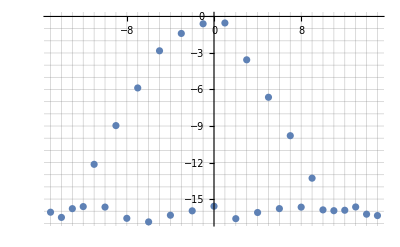

```mathematica
ListPlot[Thread[{Table[k,{k,-15,15}],Log10[Abs[Example]]}],PlotRange->All,GridLines->{Table[k,{k,-15,15}],Table[k,{k,Floor[Min[Log[Abs[Example]]]],Ceiling[Max[Log[Abs[Example]]]]}]}]
```

```mathematica
orbit = KerrGeoOrbit[a,r0,0,x];
{tp,rp,θp,ϕp}=orbit["Trajectory"];

ℰ=orbit["Energy"];
ℒ=orbit["AngularMomentum"];
Υ =orbit["Frequencies"]["Υ_θ"];

Freqs = KerrGeoFrequencies[a,r0,0,x];
Ωθ = Freqs[[2]];
Ωϕ = Freqs[[3]];
l=3;
m=2;
k = 8;
S=SpinWeightedSpheroidalHarmonicS[0,l,m,a (m Ωϕ+k Ωθ)];
Clear[Integrand]
Integrand[λ_]:=S[θp[λ],0]/ut[M,a,r0,ℰ,ℒ,θp[λ]] Cos[((m Ωϕ+k Ωθ) tp[λ]-m ϕp[λ])]dtdλ[M,a,r0,ℰ,ℒ,θp[λ]];
```

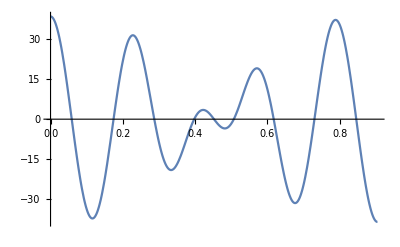

```mathematica
Plot[Integrand[λ],{λ,0,π/Υ}]
```

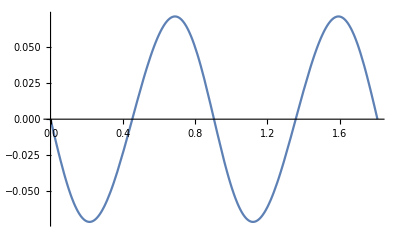

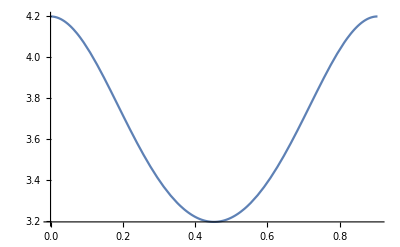

```mathematica
Plot[ Ωϕ tp[λ]-ϕp[λ],{λ,0,(2π)/Υ}]
Plot[ϕp'[λ],{λ,0,π/Υ}]
```

```mathematica
Cos[A+B]//TrigExpand
```

Cos[A] Cos[B]-Sin[A] Sin[B]

```mathematica
Cos[π-s]
```

-Cos[s]

```mathematica
Simplify[Cos[(p+n) π-ξ]//TrigExpand,Assumptions->{n∈Integers,p∈Integers}]
```

(-1)^(n+p) Cos[ξ]

```mathematica
Cos[n π/2+ξ]//TrigExpand
```

Cos[(n π)/2] Cos[ξ]-Sin[(n π)/2] Sin[ξ]

```mathematica
Simplify[{Cos[n π/2],Sin[n π/2]},Assumptions->{n∈Integers}]
```

{Cos[(n π)/2],Sin[(n π)/2]}

```mathematica
(-1)^(l+m+k+1)
```

1